# Monte Carlo Simulation using Mathematica

## Daniel Moore

I have used Monte Carlo Simulation for years, but I' ve always used other platforms that are more naturally suited to it (JMP, Matlab, R, even Excel). Mathematica is a tool that I have always used for more pure Mathematics - solving equations, etc. - and not for statistical modeling work. But there’s no reason that it couldn’t be used for Monte Carlo Simulations! It has all of the built in tools and the quick calculations for it.
So, below is my quick example of a Monte Carlo Simulation (of CPU temperatures for a computer - hence the Fan/NoFan temp rise over ambient factors.

## Input Parameters for Simulation

```mathematica
EV3BSoCPowerMu = 0.767;
EV3BSoCPowerSigma = 0.05;
EV3BClipped = 2.2;
EV3BPDAllowanceMu = 0.83;
EV3BPDAllowanceSigma = 0.04;
EV3BOffsetMu = 0.03;
EV3BOffsetSigma = 0.09;
EV3BPowerImp = -0.16;
EV3ASoCPowerMu = 0.77;
EV3ASoCPowerSigma = 0.05;
EV3AClipped = 2.5;
EV3APDAllowanceMu = 0.88;
EV3APDAllowanceSigma = 0.04;
EV3AOffsetMu = 0.03;
EV3AOffsetSigma = 0.09;
EV3APowerImp = -0.16;
EV2SoCPowerMu = 0.78;
EV2SoCPowerSigma = 0.05;
EV2Clipped = 2.52;
EV2PDAllowanceMu = 0.88;
EV2PDAllowanceSigma = 0.04;
EV2OffsetMu = 0.12;
EV2OffsetSigma = 0.06;
EV2PowerImp = 0;
SimulateNumber = 100000;
```

## Do Simulations

```mathematica
EV3BSoC= RandomVariate[TruncatedDistribution[{0,EV3BClipped},LogNormalDistribution[EV3BSoCPowerMu,EV3BSoCPowerSigma]],SimulateNumber];
EV2SoC= RandomVariate[TruncatedDistribution[{0,EV2Clipped},LogNormalDistribution[EV2SoCPowerMu,EV2SoCPowerSigma]],SimulateNumber];
EV3ASoC= RandomVariate[TruncatedDistribution[{0,EV3AClipped},LogNormalDistribution[EV3ASoCPowerMu,EV3ASoCPowerSigma]],SimulateNumber];
CoPopEV3B = EV3BSoC + RandomVariate[NormalDistribution[EV3BPDAllowanceMu,EV3BPDAllowanceSigma], SimulateNumber] +  RandomVariate[NormalDistribution[EV3BOffsetMu,EV3BOffsetSigma], SimulateNumber] +RandomVariate[NormalDistribution[EV3BPowerImp,0.000000000001], SimulateNumber];
CoPopEV3A = EV3ASoC + RandomVariate[NormalDistribution[EV3APDAllowanceMu,EV3APDAllowanceSigma], SimulateNumber] +  RandomVariate[NormalDistribution[EV3AOffsetMu,EV3AOffsetSigma], SimulateNumber] +RandomVariate[NormalDistribution[EV3APowerImp,0.000000000001], SimulateNumber];
CoPopEV2 = EV2SoC + RandomVariate[NormalDistribution[EV2PDAllowanceMu,EV2PDAllowanceSigma], SimulateNumber] +  RandomVariate[NormalDistribution[EV2OffsetMu,EV2OffsetSigma], SimulateNumber] +RandomVariate[NormalDistribution[EV2PowerImp,0.000000000001], SimulateNumber];
```

## Show Graphs

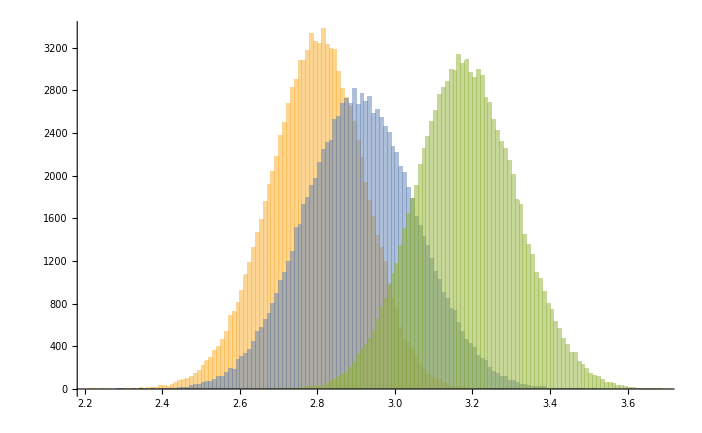

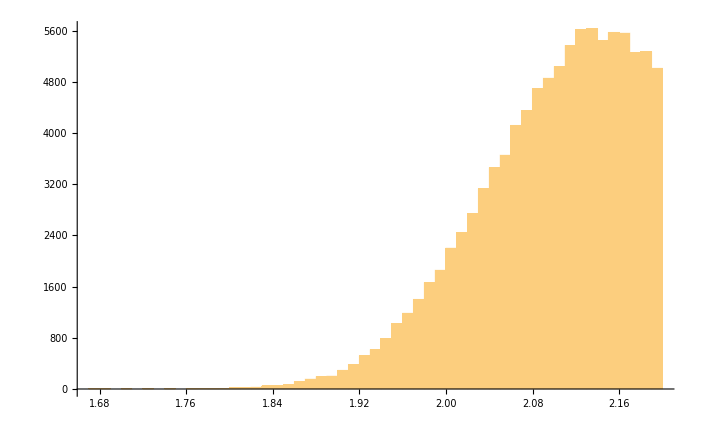

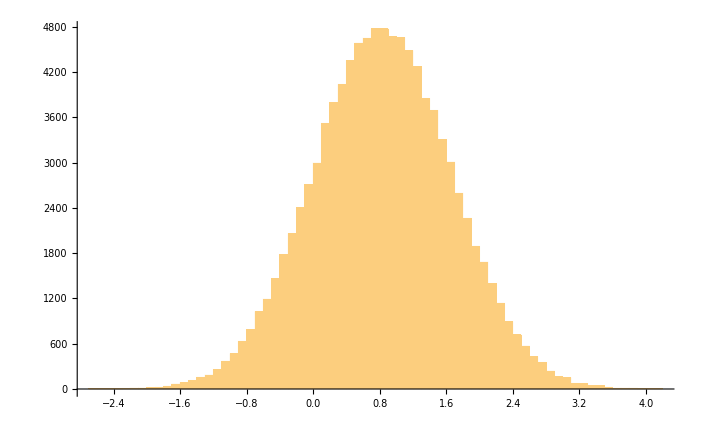

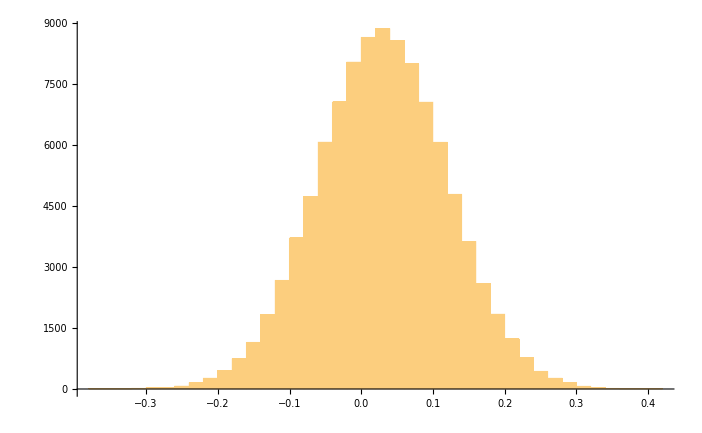

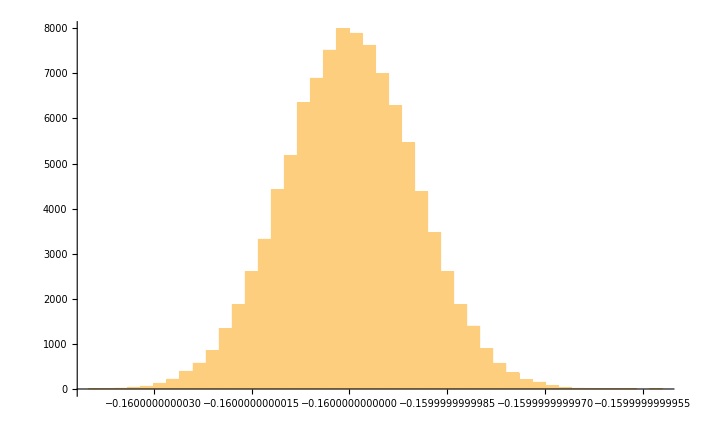

{2.69195,2.93373,2.97255,3.01847,3.09455,3.18132,3.27068,3.35075,3.39994,3.44203,3.68525}

{2.28851,2.62901,2.67386,2.72633,2.81313,2.91055,3.00938,3.09916,3.15374,3.19983,3.51849}

{2.21097,2.54972,2.59088,2.63811,2.71584,2.79881,2.87933,2.94898,2.98893,3.02418,3.27192}

```mathematica
Histogram[{CoPopEV3B, CoPopEV3A,CoPopEV2},100]
Histogram[EV3BSoC,50]
Histogram[RandomVariate[NormalDistribution[EV3BPDAllowanceMu,EV3BPDAllowanceMu],SimulateNumber],50]
Histogram[RandomVariate[NormalDistribution[EV3BOffsetMu,EV3BOffsetSigma],SimulateNumber],50]
Histogram[RandomVariate[NormalDistribution[EV3BPowerImp,0.000000000001],SimulateNumber],50]
Quantile[CoPopEV2, {0, 0.025,0.050,0.10, 0.25, 0.50, 0.75, 0.90, 0.95, 0.975, 1}]
Quantile[CoPopEV3A, {0, 0.025,0.050,0.10, 0.25, 0.50, 0.75, 0.90, 0.95, 0.975, 1}]
Quantile[CoPopEV3B, {0, 0.025,0.050,0.10, 0.25, 0.50, 0.75, 0.90, 0.95, 0.975, 1}]
```